# Noisy Intermittent Feeding Model

Version : 15/01/2026

## Two Species Case: abundances x time

### Global Parameters

```mathematica
(*----------------Parameters----------------*)

Params={
NumSpecies=2,(*Number of Species*)
r1=1.,(*Growth rate 1*)
r2=1.,(*Growth rate 2*)
c1=.75,(*Clearance rate 1*)
c2=.85,(*Clearance rate 2*)
k=1000,(*Carrying capacity*)
n0=10^(-2)k,(*Initial Condition*)
tfim=1000,(*Final time*)
frac1=0.2(*Fraction in the food of species 1*)
};

t0=0;(*Initial time*)

cor1=RGBColor["#D81B60"]; (*Good color 1 for pictures*)
cor2=RGBColor["#1E88E5"];(*Good color 2 for pictures*)
```

### a) Noisy τ

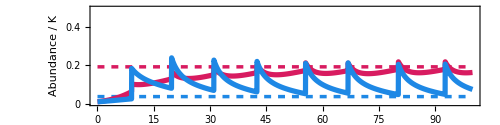

```mathematica
(*----------------Parameters----------------*)

τ0=12; (*MEAN Time between meals*)
sd=0.2τ0; (*Standard deviation of τ*)
nf=200;(*Total amount of microbes in each meal*)

(*----------------Solution----------------*)

dist=NormalDistribution[τ0,sd];

times=Accumulate@RandomVariate[dist,Round[tfim/τ0]+1];
cond=(t==#)&/@times;

sol=
NDSolve[
{n1'[t]==r1*n1[t](1-(n1[t]+n2[t])/k)-c1*n1[t],(*Equation species 1*)
n2'[t]==r2*n2[t](1-(n1[t]+n2[t])/k)-c2*n2[t],(*Equation species 2*)
n1[0]==n0,
n2[0]==n0,
WhenEvent[Evaluate[cond],
{
n1[t]->n1[t]+nf(frac1),
n2[t]->n2[t]+nf(1-frac1)
}
]
},
{n1,n2},
{t,t0,tfim},
(*MaxStepSize->0.001,*)
Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->4}
}];

(*----------------Figures----------------*)

Solution1=Show[
Plot[{193/k,37.2/k},{t,0,100},PlotStyle->{{cor1,Thickness[0.005],Dashed},{cor2,Thickness[0.005],Dashed}},Axes->False],
Plot[Evaluate[({n1[t],n2[t]}/(k)/.#)&/@sol],{t,0,100},(*PlotLegends->Placed[SwatchLegend[{"n_1","n_2"}],{0.08,0.75}],*)LabelStyle->{FontSize->18,FontColor->Black},PlotStyle->{{cor1,Thickness[0.0075]},{cor2,Thickness[0.0075]}}],
PlotRange->{0,0.5},
Frame->True,
FrameStyle->Directive[Black,FontSize->16],FrameLabel->{"Time","Abundance / K"},
AspectRatio->1/4,
ImageSize->500,
FrameTicks->{{{0,0.2,0.4},None},{Automatic,None}},
ImagePadding->{{50,10}, {50,1}}]
```

### b) Noisy nf

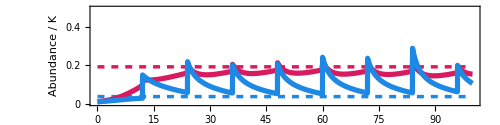

```mathematica
(*----------------Parameters----------------*)

τ0=12; (*MEAN Time between meals*)
nf=200;(*Total amount of microbes in each meal*)
sd=0.2nf; (*Standard deviation of τ*)

(*----------------Solution----------------*)

dist=TruncatedDistribution[{0,+∞},NormalDistribution[nf,sd]];
nfList=RandomVariate[dist,Round[tfim/τ0]+1];
j=0;
sol=
NDSolve[
{n1'[t]==r1*n1[t](1-(n1[t]+n2[t])/k)-c1*n1[t],(*Equation species 1*)
n2'[t]==r2*n2[t](1-(n1[t]+n2[t])/k)-c2*n2[t],(*Equation species 2*)
n1[0]==n0,
n2[0]==n0,
WhenEvent[Mod[t,τ0],
{
j++,
n1[t]->n1[t]+nfList⟦j⟧(frac1),
n2[t]->n2[t]+nfList⟦j⟧(1-frac1)
}
]
},
{n1,n2},
{t,t0,tfim},
(*MaxStepSize->0.001,*)
Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->4}
}];

(*----------------Figures----------------*)

Solution1=Show[
Plot[{193/k,37.2/k},{t,0,100},PlotStyle->{{cor1,Thickness[0.005],Dashed},{cor2,Thickness[0.005],Dashed}},Axes->False],
Plot[Evaluate[({n1[t],n2[t]}/(k)/.#)&/@sol],{t,0,100},(*PlotLegends->Placed[SwatchLegend[{"n_1","n_2"}],{0.08,0.75}],*)LabelStyle->{FontSize->18,FontColor->Black},PlotStyle->{{cor1,Thickness[0.0075]},{cor2,Thickness[0.0075]}}],
PlotRange->{0,0.5},
Frame->True,
FrameStyle->Directive[Black,FontSize->16],FrameLabel->{"Time","Abundance / K"},
AspectRatio->1/4,
ImageSize->500,
FrameTicks->{{{0,0.2,0.4},None},{Automatic,None}},
ImagePadding->{{50,10}, {50,1}}]
```

### c) Noisy nf and τ

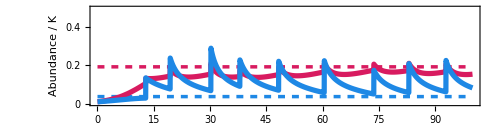

```mathematica
(*----------------Parameters----------------*)

τ0=12; (*MEAN Time between meals*)
nf=200;(*Total amount of microbes in each meal*)
sdNF=0.2nf; (*Standard deviation of τ*)
sdTAU=0.2τ0; (*Standard deviation of τ*)

(*----------------Solution----------------*)

distNF=TruncatedDistribution[{0,+∞},NormalDistribution[nf,sdNF]];
nfList=RandomVariate[distNF,Round[tfim/τ0]+1];

distTAU=TruncatedDistribution[{0,+∞},NormalDistribution[τ0,sdTAU]];
times=Accumulate@RandomVariate[distTAU,Round[tfim/τ0]+1];
cond=(t==#)&/@times;

j=0;
sol=
NDSolve[
{n1'[t]==r1*n1[t](1-(n1[t]+n2[t])/k)-c1*n1[t],(*Equation species 1*)
n2'[t]==r2*n2[t](1-(n1[t]+n2[t])/k)-c2*n2[t],(*Equation species 2*)
n1[0]==n0,
n2[0]==n0,
WhenEvent[Evaluate[cond],
{
j++,
n1[t]->n1[t]+nfList⟦j⟧(frac1),
n2[t]->n2[t]+nfList⟦j⟧(1-frac1)
}
]
},
{n1,n2},
{t,t0,tfim},
(*MaxStepSize->0.001,*)
Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->4}
}];

(*----------------Figures----------------*)

Solution1=Show[
Plot[{193/k,37.2/k},{t,0,100},PlotStyle->{{cor1,Thickness[0.005],Dashed},{cor2,Thickness[0.005],Dashed}},Axes->False],
Plot[Evaluate[({n1[t],n2[t]}/(k)/.#)&/@sol],{t,0,100},(*PlotLegends->Placed[SwatchLegend[{"n_1","n_2"}],{0.08,0.75}],*)LabelStyle->{FontSize->18,FontColor->Black},PlotStyle->{{cor1,Thickness[0.0075]},{cor2,Thickness[0.0075]}}],
PlotRange->{0,0.5},
Frame->True,
FrameStyle->Directive[Black,FontSize->16],FrameLabel->{"Time","Abundance / K"},
AspectRatio->1/4,
ImageSize->500,
FrameTicks->{{{0,0.2,0.4},None},{Automatic,None}},
ImagePadding->{{50,10}, {50,1}}]
```

### d) Noisy f_1

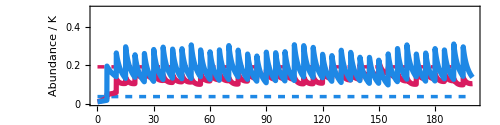

```mathematica
(*----------------Parameters----------------*)

τ0=5; (*MEAN Time between meals*)
nf=200;(*Total amount of microbes in each meal*)

sd=1frac1; (*Standard deviation of τ*)

(*----------------Solution----------------*)

κ=10;
dist=BetaDistribution[1+κ frac1,1+κ (1-frac1)];
frac1List=RandomVariate[dist,Round[tfim/τ0]+1];

j=0;
sol=
NDSolve[
{n1'[t]==r1*n1[t](1-(n1[t]+n2[t])/k)-c1*n1[t],(*Equation species 1*)
n2'[t]==r2*n2[t](1-(n1[t]+n2[t])/k)-c2*n2[t],(*Equation species 2*)
n1[0]==n0,
n2[0]==n0,
WhenEvent[Mod[t,τ0],
{
j++,
n1[t]->n1[t]+nf(frac1List⟦j⟧),
n2[t]->n2[t]+nf(1-frac1List⟦j⟧),
AppendTo[arrows,{{n1[t]-nf*frac1List⟦j⟧,n2[t]-nf*(1-frac1List⟦j⟧)},{n1[t],n2[t]}}],
}
]
},
{n1,n2},
{t,t0,tfim},
(*MaxStepSize->0.001,*)
Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->4}
}];

(*----------------Figures----------------*)

Solution1=Show[
Plot[{193/k,37.2/k},{t,0,200},PlotStyle->{{cor1,Thickness[0.005],Dashed},{cor2,Thickness[0.005],Dashed}},Axes->False],
Plot[Evaluate[({n1[t],n2[t]}/(k)/.#)&/@sol],{t,0,200},(*PlotLegends->Placed[SwatchLegend[{"n_1","n_2"}],{0.08,0.75}],*)LabelStyle->{FontSize->18,FontColor->Black},PlotStyle->{{cor1,Thickness[0.0075]},{cor2,Thickness[0.0075]}}],
PlotRange->{0,0.5},
Frame->True,
FrameStyle->Directive[Black,FontSize->16],FrameLabel->{"Time","Abundance / K"},
AspectRatio->1/4,
ImageSize->500,
FrameTicks->{{{0,0.2,0.4},None},{Automatic,None}},
ImagePadding->{{50,10}, {50,1}}]
```

## Heatmap of - Noisy TAU

### Global Parameters

```mathematica
(*----------------Parameters----------------*)

Params={
NumSpecies=2,(*Number of Species*)
r1=1.,(*Growth rate 1*)
r2=1.,(*Growth rate 2*)
c1=0.75,(*Clearance rate 1*)
c2=0.85,(*Clearance rate 2*)
k=1000,(*Carrying capacity*)
n0=10,(*Initial Condition*)
tfim=1500,(*Final time*)
frac1=0.2,(*Fraction in the food of species 1*)
sdFactorTau=0.1
};

t0=0;(*Initial time*)

dir=NotebookDirectory[]<>"HeatMap-Data2-noisyTAU-sd-0.1\\";
```

### Exporting data

```mathematica
LaunchKernels[12](*Launching kernels for parallel evaluation*)
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
CloseKernels[](*Closing kernels after parallel evaluation*)
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
Do[

Export[dir<>"params.txt",Params,"TABLE"];

dir=NotebookDirectory[]<>"HeatMap-Data2-noisyTAU-sd-"<>ToString[sdFactorTau]<>"\\";

eqs={n1'[t]==r1*n1[t](1-(n1[t]+n2[t])/k)-c1*n1[t],n2'[t]==r2*n2[t](1-(n1[t]+n2[t])/k)-c2*n2[t]};
{n01,n02}={n0,n0};
ini={n1[0]==n0,n2[0]==n0};
solNoFeed=NDSolve[Join[eqs,ini],{n1,n2},{t,0,tfim}];

SetSharedVariable[resNumericTab];

Do[
If[FileExistsQ[dir<>"DIV-tau-"<>ToString[τ]<>".txt"],
resNumericTab=Import[dir<>"DIV-tau-"<>ToString[τ]<>".txt","TABLE"],
resNumericTab={}];

ParallelDo[
nf=nfx;
dist=TruncatedDistribution[{0,+∞},NormalDistribution[τ,sdFactorTau*τ]];
times=Accumulate@RandomVariate[dist,Round[tfim/τ]+1];
cond=(t==#)&/@times;
sol=
NDSolve[
{n1'[t]==r1*n1[t](1-(n1[t]+n2[t])/k)-c1*n1[t],(*Equation species 1*)
n2'[t]==r2*n2[t](1-(n1[t]+n2[t])/k)-c2*n2[t],(*Equation species 2*)
n1[0]==n0,
n2[0]==n0,
WhenEvent[Evaluate[cond],
{n1[t]->n1[t]+nf(frac1),
n2[t]->n2[t]+nf(1-frac1)}]},
{n1,n2},
{t,t0,tfim},
(*MaxStepSize->0.001,*)
Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->4}}
];

nCycles=50;

res=Quiet@NIntegrate[Evaluate[(-(n1[t]/(n1[t]+n2[t]))*Log[(n1[t]/(n1[t]+n2[t]))]-(n2[t]/(n1[t]+n2[t]))*Log[(n2[t]/(n1[t]+n2[t]))])/.First[sol]],{t,tfim-nCycles*τ,tfim},Method->"Trapezoidal"]/(nCycles*τ);

AppendTo[resNumericTab,{nfx,res}]
,{nfx,2,200}];

Export[dir<>"DIV-tau-"<>ToString[τ]<>".txt",resNumericTab,"TABLE"]

,{τ,11.95,0.1,-0.15(*15/100*)}]

,{sdFactorTau,{0.3,0.5,0.7}}]
```

### Importing Data

```mathematica
dir=NotebookDirectory[]<>"HeatMap-Data2-noisyTAU-sd-0.7\\";

τ0=0.1;
intτ=0.15;

tab=Table[
dat=Sort@Import[dir<>"DIV-tau-"<>ToString[τ]<>".txt","TABLE"];
nf=dat⟦All,1⟧;
Shannon=dat⟦All,2⟧;
Transpose[{Table[τ,{Length[nf]}],nf,Shannon}],
{τ,τ0,12,intτ}];
tab2=Flatten[tab,1];
```

### Heatmap

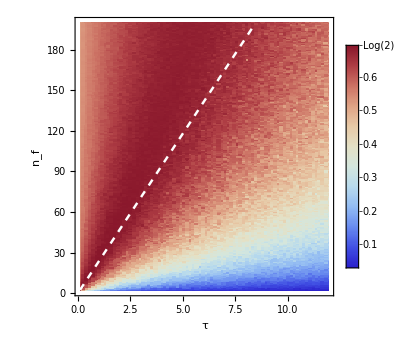

```mathematica
heatmap=ListDensityPlot[tab2,InterpolationOrder->0,
PlotLegends->BarLegend[Automatic,Ticks->{0.1,0.2,0.3,0.4,0.5,0.6,{.693,"Log(2)"}},LegendMarkerSize->250],
ColorFunction->ColorData["ThermometerColors"],
ColorFunctionScaling->True,
ImageSize->350,Frame->True,FrameStyle->Directive[Black,FontSize->18],FrameLabel->{"τ","n_f","Shannon Diversity "},
LabelStyle->Directive[Black,FontSize->16]
];

α=(k (c2 r1-c1 r2) (c2 frac1-c1 (1-frac1)+(1-frac1)r1-frac1 r2))/(2 ((1-frac1) r1-frac1 r2)^2);

Show[heatmap,
(*ListLinePlot[peaks,PlotStyle->{White,PointSize->0.001,Thickness[0.0075]}],*)
Plot[α τ,{τ,0.1,8.45},PlotStyle->{White,Dashed,Thickness[0.005]}]
]
```

## Heatmap of - Noisy NF

### Global Parameters

```mathematica
(*----------------Parameters----------------*)

Params={
NumSpecies=2,(*Number of Species*)
r1=1.,(*Growth rate 1*)
r2=1.,(*Growth rate 2*)
c1=0.75,(*Clearance rate 1*)
c2=0.85,(*Clearance rate 2*)
k=1000,(*Carrying capacity*)
n0=10,(*Initial Condition*)
tfim=1500,(*Final time*)
frac1=0.2,(*Fraction in the food of species 1*)
sdFactorNF=0.1
};

t0=0;(*Initial time*)

dir=NotebookDirectory[]<>"HeatMap-Data2-noisyNF-sd-0.1\\";
```

### Exporting data

```mathematica
LaunchKernels[12](*Launching kernels for parallel evaluation*)
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
CloseKernels[](*Closing kernels after parallel evaluation*)
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
Do[

Export[dir<>"params.txt",Params,"TABLE"];

dir=NotebookDirectory[]<>"HeatMap-Data2-noisyNF-sd-"<>ToString[sdFactorNF]<>"\\";

eqs={n1'[t]==r1*n1[t](1-(n1[t]+n2[t])/k)-c1*n1[t],n2'[t]==r2*n2[t](1-(n1[t]+n2[t])/k)-c2*n2[t]};
{n01,n02}={n0,n0};
ini={n1[0]==n0,n2[0]==n0};
solNoFeed=NDSolve[Join[eqs,ini],{n1,n2},{t,0,tfim}];

SetSharedVariable[resNumericTab];

Do[
If[FileExistsQ[dir<>"DIV-tau-"<>ToString[τ]<>".txt"],
resNumericTab=Import[dir<>"DIV-tau-"<>ToString[τ]<>".txt","TABLE"],
resNumericTab={}];

ParallelDo[
nf=nfx;
dist=TruncatedDistribution[{0,+∞},NormalDistribution[nf,sdFactorNF*nf]];
nfList=RandomVariate[dist,Round[tfim/τ]+1];
j=0;
sol=
NDSolve[
{n1'[t]==r1*n1[t](1-(n1[t]+n2[t])/k)-c1*n1[t],(*Equation species 1*)
n2'[t]==r2*n2[t](1-(n1[t]+n2[t])/k)-c2*n2[t],(*Equation species 2*)
n1[0]==n0,
n2[0]==n0,
WhenEvent[Mod[t,τ],
{j++,
n1[t]->n1[t]+nfList⟦j⟧(frac1),
n2[t]->n2[t]+nfList⟦j⟧(1-frac1)}]},
{n1,n2},
{t,t0,tfim},
(*MaxStepSize->0.001,*)
Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->4}}
];

nCycles=50;

res=Quiet@NIntegrate[Evaluate[(-(n1[t]/(n1[t]+n2[t]))*Log[(n1[t]/(n1[t]+n2[t]))]-(n2[t]/(n1[t]+n2[t]))*Log[(n2[t]/(n1[t]+n2[t]))])/.First[sol]],{t,tfim-nCycles*τ,tfim},Method->"Trapezoidal"]/(nCycles*τ);

AppendTo[resNumericTab,{nfx,res}]
,{nfx,2,200}];

Export[dir<>"DIV-tau-"<>ToString[τ]<>".txt",resNumericTab,"TABLE"]

,{τ,11.95,0.1,-0.15(*15/100*)}]

,{sdFactorNF,{0.7}}]
```

### Importing Data

```mathematica
dir=NotebookDirectory[]<>"HeatMap-Data2-noisyNF-sd-0.7\\";

τ0=0.1;
intτ=0.15;

tab=Table[
dat=Sort@Import[dir<>"DIV-tau-"<>ToString[τ]<>".txt","TABLE"];
nf=dat⟦All,1⟧;
Shannon=dat⟦All,2⟧;
Transpose[{Table[τ,{Length[nf]}],nf,Shannon}],
{τ,τ0,12,intτ}];
tab2=Flatten[tab,1];
```

### Heatmap

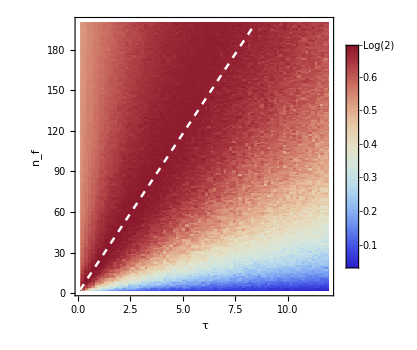

```mathematica
heatmap=ListDensityPlot[tab2,InterpolationOrder->0,
PlotLegends->BarLegend[Automatic,Ticks->{0.1,0.2,0.3,0.4,0.5,0.6,{.693,"Log(2)"}},LegendMarkerSize->250],
ColorFunction->ColorData["ThermometerColors"],
ColorFunctionScaling->True,
ImageSize->350,Frame->True,FrameStyle->Directive[Black,FontSize->18],FrameLabel->{"τ","n_f","Shannon Diversity "},
LabelStyle->Directive[Black,FontSize->16]
];

α=(k (c2 r1-c1 r2) (c2 frac1-c1 (1-frac1)+(1-frac1)r1-frac1 r2))/(2 ((1-frac1) r1-frac1 r2)^2);

Show[heatmap,
(*ListLinePlot[peaks,PlotStyle->{White,PointSize->0.001,Thickness[0.0075]}],*)
Plot[α τ,{τ,0.1,8.45},PlotStyle->{White,Dashed,Thickness[0.005]}]
]
```

## Heatmap of - Noisy TAU and NF

### Global Parameters

```mathematica
(*----------------Parameters----------------*)

Params={
NumSpecies=2,(*Number of Species*)
r1=1.,(*Growth rate 1*)
r2=1.,(*Growth rate 2*)
c1=0.75,(*Clearance rate 1*)
c2=0.85,(*Clearance rate 2*)
k=1000,(*Carrying capacity*)
n0=10,(*Initial Condition*)
tfim=1500,(*Final time*)
frac1=0.2,(*Fraction in the food of species 1*)
sdFactorTau=0.1,
sdFactorNF=0.1
};

t0=0;(*Initial time*)

dir=NotebookDirectory[]<>"HeatMap-Data2-noisyTAUandNF-sd-0.5\\";
```

### Exporting data

```mathematica
LaunchKernels[12](*Launching kernels for parallel evaluation*)
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
CloseKernels[](*Closing kernels after parallel evaluation*)
```

{}

```mathematica
Do[

Export[dir<>"params.txt",Params,"TABLE"];

dir=NotebookDirectory[]<>"HeatMap-Data2-noisyTAUandNF-sd-"<>ToString[sdFactor]<>"\\";

eqs={n1'[t]==r1*n1[t](1-(n1[t]+n2[t])/k)-c1*n1[t],n2'[t]==r2*n2[t](1-(n1[t]+n2[t])/k)-c2*n2[t]};
{n01,n02}={n0,n0};
ini={n1[0]==n0,n2[0]==n0};
solNoFeed=NDSolve[Join[eqs,ini],{n1,n2},{t,0,tfim}];

SetSharedVariable[resNumericTab];

Do[
If[FileExistsQ[dir<>"DIV-tau-"<>ToString[τ]<>".txt"],
resNumericTab=Import[dir<>"DIV-tau-"<>ToString[τ]<>".txt","TABLE"],
resNumericTab={}];

ParallelDo[
nf=nfx;
distNF=TruncatedDistribution[{0,+∞},NormalDistribution[nf,sdFactor*nf]];
nfList=RandomVariate[distNF,Round[tfim/τ]+1];

distTAU=TruncatedDistribution[{0,+∞},NormalDistribution[τ,sdFactor*τ]];
times=Accumulate@RandomVariate[distTAU,Round[tfim/τ]+1];
cond=(t==#)&/@times;
j=0;
sol=
NDSolve[
{n1'[t]==r1*n1[t](1-(n1[t]+n2[t])/k)-c1*n1[t],(*Equation species 1*)
n2'[t]==r2*n2[t](1-(n1[t]+n2[t])/k)-c2*n2[t],(*Equation species 2*)
n1[0]==n0,
n2[0]==n0,
WhenEvent[Evaluate[cond],
{j++,
n1[t]->n1[t]+nfList⟦j⟧(frac1),
n2[t]->n2[t]+nfList⟦j⟧(1-frac1)}]},
{n1,n2},
{t,t0,tfim},
(*MaxStepSize->0.001,*)
Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->4}}
];

nCycles=50;

res=Quiet@NIntegrate[Evaluate[(-(n1[t]/(n1[t]+n2[t]))*Log[(n1[t]/(n1[t]+n2[t]))]-(n2[t]/(n1[t]+n2[t]))*Log[(n2[t]/(n1[t]+n2[t]))])/.First[sol]],{t,tfim-nCycles*τ,tfim},Method->"Trapezoidal"]/(nCycles*τ);

AppendTo[resNumericTab,{nfx,res}]
,{nfx,2,200}];

Export[dir<>"DIV-tau-"<>ToString[τ]<>".txt",resNumericTab,"TABLE"]

,{τ,11.95,10.45,-0.15(*15/100*)}]

,{sdFactor,{0.5}}]
```

```mathematica
resNumericTab
```

```mathematica
dir
```

C:\Users\vmarquioni\Dropbox\Research\PostDoc - Marseille - 2024\Papers\Paper 1 - diversity\Simulations\HeatMap-Data2-noisyTAUandNF-sd-0.3\

```mathematica
Export[dir<>"DIV-tau-"<>ToString[0.1]<>".txt",Sort@resNumericTab,"TABLE"]
```

C:\Users\vmarquioni\Dropbox\Research\PostDoc - Marseille - 2024\Papers\Paper 1 - diversity\Simulations\HeatMap-Data2-noisyTAUandNF-sd-0.3\DIV-tau-0.1.txt

### Importing Data

```mathematica
dir=NotebookDirectory[]<>"HeatMap-Data2-noisyTAUandNF-sd-0.5\\";

τ0=0.1;
intτ=0.15;

tab=Table[
dat=Sort@Import[dir<>"DIV-tau-"<>ToString[τ]<>".txt","TABLE"];
nf=dat⟦All,1⟧;
Shannon=dat⟦All,2⟧;
Transpose[{Table[τ,{Length[nf]}],nf,Shannon}],
{τ,τ0,12,intτ}];
tab2=Flatten[tab,1];
```

### Heatmap

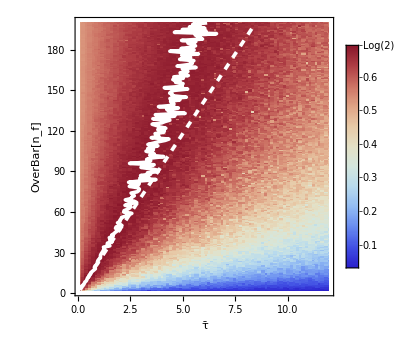

```mathematica
heatmap=ListDensityPlot[tab2,InterpolationOrder->0,
PlotLegends->BarLegend[Automatic,Ticks->{0.1,0.2,0.3,0.4,0.5,0.6,{.693,"Log(2)"}},LegendMarkerSize->250],
ColorFunction->ColorData["ThermometerColors"],
ColorFunctionScaling->True,
ImageSize->350,Frame->True,FrameStyle->Directive[Black,FontSize->18],FrameLabel->{"τ̄","OverBar[n_f]","Shannon Diversity "},
LabelStyle->Directive[Black,FontSize->16]
];

α=(k (c2 r1-c1 r2) (c2 frac1-c1 (1-frac1)+(1-frac1)r1-frac1 r2))/(2 ((1-frac1) r1-frac1 r2)^2);

Show[heatmap,
(*ListLinePlot[nfPeak,PlotStyle->{White,PointSize->0.001,Thickness[0.0075]}],*)
Plot[α τ,{τ,0.1,8.45},PlotStyle->{White,Dashed,Thickness[0.0075]}]
]
```

## Heatmap of - Noisy f1

### Global Parameters

```mathematica
(*----------------Parameters----------------*)

Params={
NumSpecies=2,(*Number of Species*)
r1=1.,(*Growth rate 1*)
r2=1.,(*Growth rate 2*)
c1=0.75,(*Clearance rate 1*)
c2=0.85,(*Clearance rate 2*)
k=1000,(*Carrying capacity*)
n0=10,(*Initial Condition*)
tfim=1500,(*Final time*)
frac1=0.2,(*Fraction in the food of species 1*)
sdFactorF1=0.1
};

t0=0;(*Initial time*)
```

### Exporting data

```mathematica
LaunchKernels[12](*Launching kernels for parallel evaluation*)
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
CloseKernels[](*Closing kernels after parallel evaluation*)
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
Do[

dir=NotebookDirectory[]<>"HeatMap-Data3-noisyF1-kapa-"<>ToString[κ]<>"\\";

eqs={n1'[t]==r1*n1[t](1-(n1[t]+n2[t])/k)-c1*n1[t],n2'[t]==r2*n2[t](1-(n1[t]+n2[t])/k)-c2*n2[t]};
{n01,n02}={n0,n0};
ini={n1[0]==n0,n2[0]==n0};
solNoFeed=NDSolve[Join[eqs,ini],{n1,n2},{t,0,tfim}];

SetSharedVariable[resNumericTab];

Do[
If[FileExistsQ[dir<>"DIV-tau-"<>ToString[τ]<>".txt"],
resNumericTab=Import[dir<>"DIV-tau-"<>ToString[τ]<>".txt","TABLE"],
resNumericTab={}];

ParallelDo[
nf=nfx;
dist=BetaDistribution[1+κ frac1,1+κ (1-frac1)];
frac1List=RandomVariate[dist,Round[tfim/τ]+1];
j=0;
sol=
NDSolve[
{n1'[t]==r1*n1[t](1-(n1[t]+n2[t])/k)-c1*n1[t],(*Equation species 1*)
n2'[t]==r2*n2[t](1-(n1[t]+n2[t])/k)-c2*n2[t],(*Equation species 2*)
n1[0]==n0,
n2[0]==n0,
WhenEvent[Mod[t,τ],
{j++,
n1[t]->n1[t]+nf(frac1List⟦j⟧),
n2[t]->n2[t]+nf(1-frac1List⟦j⟧)}]},
{n1,n2},
{t,t0,tfim},
(*MaxStepSize->0.001,*)
Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->4}}
];

nCycles=50;

res=Quiet@NIntegrate[Evaluate[(-(n1[t]/(n1[t]+n2[t]))*Log[(n1[t]/(n1[t]+n2[t]))]-(n2[t]/(n1[t]+n2[t]))*Log[(n2[t]/(n1[t]+n2[t]))])/.First[sol]],{t,tfim-nCycles*τ,tfim},Method->"Trapezoidal"]/(nCycles*τ);

AppendTo[resNumericTab,{nfx,res}]
,{nfx,2,200}];

Export[dir<>"DIV-tau-"<>ToString[τ]<>".txt",resNumericTab,"TABLE"]

,{τ,11.95,0.1,-0.15(*15/100*)}]

,{κ,{5}}]
```

### Importing Data

```mathematica
κ=1000;
dir=NotebookDirectory[]<>"HeatMap-Data3-noisyF1-kapa-"<>ToString[κ]<>"\\";

τ0=0.1;
intτ=0.15;

tab=Table[
dat=Sort@Import[dir<>"DIV-tau-"<>ToString[τ]<>".txt","TABLE"];
nf=dat⟦All,1⟧;
Shannon=dat⟦All,2⟧;
Transpose[{Table[τ,{Length[nf]}],nf,Shannon}],
{τ,τ0,12,intτ}];
tab2=Flatten[tab,1];
```

### Heatmap

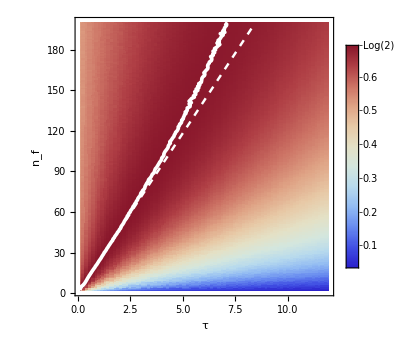

```mathematica
heatmap=ListDensityPlot[tab2,InterpolationOrder->0,
PlotLegends->BarLegend[Automatic,Ticks->{0.1,0.2,0.3,0.4,0.5,0.6,{.693,"Log(2)"}},LegendMarkerSize->250],
ColorFunction->ColorData["ThermometerColors"],
ColorFunctionScaling->True,
ImageSize->350,Frame->True,FrameStyle->Directive[Black,FontSize->18],FrameLabel->{"τ","n_f","Shannon Diversity "},
LabelStyle->Directive[Black,FontSize->16]
];


dist=BetaDistribution[1+κ frac1,1+ κ(1-frac1)];
frac1Corrected=Mean@dist;
α=(k (c2 r1-c1 r2) (c2 frac1Corrected-c1 (1-frac1Corrected)+(1-frac1Corrected)r1-frac1Corrected r2))/(2 ((1-frac1Corrected) r1-frac1Corrected r2)^2);

Show[heatmap,
(*ListLinePlot[nfPeak,PlotStyle->{White,PointSize->0.001,Thickness[0.0075]}],*)
Plot[α τ,{τ,0.1,8.45},PlotStyle->{White,Dashed,Thickness[0.005]}]
]
```

## Final Heatmap Images

### Global Parameters

```mathematica
(*----------------Parameters----------------*)

Params={
r1=1.,(*Growth rate 1*)
r2=1.,(*Growth rate 2*)
c1=0.75,(*Clearance rate 1*)
c2=0.85,(*Clearance rate 2*)
k=1000,(*Carrying capacity*)
frac1=0.2,(*Fraction in the food of species 1*)
τ0=0.1;
intτ=0.15;
};
```

```mathematica
(*-----------------------------------------------*)
(*The previous codes export the heatmap data considering the "nominal" mean_Tau and mean_nf; here we recalculate these values but considering the truncated distributions.*)
(*Aux functions*)
dist[μ_,sd_]:=TruncatedDistribution[{0,+∞},NormalDistribution[μ,sd*μ]];

Print[Dynamic@τi]
Print[Dynamic@nfi]
Print[Dynamic@sd]
Do[
Do[funcτ[τi,sd]=Mean[dist[τi,sd]],{τi,τ0,12,intτ}];
Do[funcN[nfi,sd]=Mean[dist[nfi,sd]],{nfi,2,200}];
,{sd,{0.1,0.3,0.5,0.7}}];
(*-----------------------------------------------*)
```

### Importing Data

```mathematica
(*Uncomment the parts below to calculate the exact case*)

(*Noisy nf*)
(*
case="NF";
sd=0.7;
dir=NotebookDirectory[]<>"HeatMap-Data2-noisyNF-sd-"<>ToString[sd]<>"\\";
*)

(*Noisy tau*)
(*
case="TAU";
sd=0.7;
dir=NotebookDirectory[]<>"HeatMap-Data2-noisyTAU-sd-"<>ToString[sd]<>"\\";
*)

(*Noisy tau and nf*)
(*
case="TAUandNF";
sd=0.7;
dir=NotebookDirectory[]<>"HeatMap-Data2-noisyTAUandNF-sd-"<>ToString[sd]<>"\\";
*)

(*Noisy f1*)
case="f1";
κ=5;
dir=NotebookDirectory[]<>"HeatMap-Data3-noisyF1-kapa-"<>ToString[κ]<>"\\";
```

```mathematica
(*Importing*)
Which[
(*--------------------------------------------------------------*)
case=="TAU",
{tab=Table[
dat=Sort@Import[dir<>"DIV-tau-"<>ToString[τ]<>".txt","TABLE"];
nf=dat⟦All,1⟧;
Shannon=dat⟦All,2⟧;
Transpose[{Table[funcτ[τ,sd],{Length[nf]}],nf,Shannon}],
{τ,τ0,12,intτ}];
α=(k (c2 r1-c1 r2) (c2 frac1-c1 (1-frac1)+(1-frac1)r1-frac1 r2))/(2 ((1-frac1) r1-frac1 r2)^2);
tab2=Flatten[tab,1]},
(*-------------------------------------------------------------*)
case=="NF",
{tab=Table[
dat=Sort@Import[dir<>"DIV-tau-"<>ToString[τ]<>".txt","TABLE"];
nf=funcN[#,sd]&/@dat⟦All,1⟧;
Shannon=dat⟦All,2⟧;
Transpose[{Table[τ,{Length[nf]}],nf,Shannon}],
{τ,τ0,12,intτ}];
α=(k (c2 r1-c1 r2) (c2 frac1-c1 (1-frac1)+(1-frac1)r1-frac1 r2))/(2 ((1-frac1) r1-frac1 r2)^2);
tab2=Flatten[tab,1]},
(*-------------------------------------------------------------*)
case=="TAUandNF",
{tab=Table[
dat=Sort@Import[dir<>"DIV-tau-"<>ToString[τ]<>".txt","TABLE"];
nf=funcN[#,sd]&/@dat⟦All,1⟧;
Shannon=dat⟦All,2⟧;
Transpose[{Table[funcτ[τ,sd],{Length[nf]}],nf,Shannon}],
{τ,τ0,12,intτ}];
α=(k (c2 r1-c1 r2) (c2 frac1-c1 (1-frac1)+(1-frac1)r1-frac1 r2))/(2 ((1-frac1) r1-frac1 r2)^2);
tab2=Flatten[tab,1]},
(*-------------------------------------------------------------*)
case=="f1",
{tab=Table[
dat=Sort@Import[dir<>"DIV-tau-"<>ToString[τ]<>".txt","TABLE"];
nf=dat⟦All,1⟧;
Shannon=dat⟦All,2⟧;
Transpose[{Table[τ,{Length[nf]}],nf,Shannon}],
{τ,τ0,12,intτ}];
frac1New=Mean@BetaDistribution[1+κ frac1,1+κ(1-frac1)];
α=(k (c2 r1-c1 r2) (c2 frac1New-c1 (1-frac1New)+(1-frac1New)r1-frac1New r2))/(2 ((1-frac1New) r1-frac1New r2)^2);
tab2=Flatten[tab,1]}
];
```

### Heatmap

```mathematica
(*--------------- Estimating the diversity peak values for the MDS ------------*)
order=10;
params=Table[a[i],{i,0,order}];
pol=Total[params*Table[x^i,{i,0,order}]];
nfPeak=Table[
aux=Take[Transpose[tab]⟦j-1⟧⟦All,{1,3}⟧,61];
fit=NonlinearModelFit[aux,pol,params,x];
{ArgMax[{fit[x],τ0<=x<=τ0+60*intτ},x],j}
,{j,2,200}];
(*------------------------------------------------------------------------*)
```

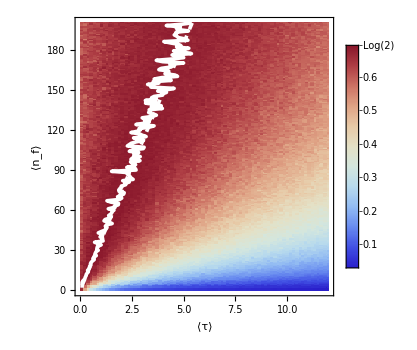

```mathematica
heatmap=ListDensityPlot[tab2,InterpolationOrder->0,
PlotLegends->BarLegend[Automatic,Ticks->{0.1,0.2,0.3,0.4,0.5,0.6,{.693,"Log(2)"}},LegendMarkerSize->250],
ColorFunction->ColorData["ThermometerColors"],
ColorFunctionScaling->True,
ImageSize->350,Frame->True,
FrameStyle->Directive[Black,FontSize->18],
FrameLabel->{"⟨τ⟩","⟨n_f⟩","Shannon Diversity "},
LabelStyle->Directive[Black,FontSize->16],
PlotRange->{{0,12},{0,200}}
];

Show[heatmap,
ListLinePlot[nfPeak,PlotStyle->{White,PointSize->0.001,Thickness[0.0075]}],
Plot[α τ,{τ,0.1,8.45},PlotStyle->{White,Dashed,Thickness[0.0075]}]
]
```